```mathematica
Needs["Utilities`"]
Needs["Kappamin`"]
Needs["Constants`"]
```

### Without Extrapolation to core T

#### Load EL dicts

```mathematica
FeELOutputDictSI =ReadIt[NotebookDirectory[]<>"../compute energy loss/FeELOutputDictSI"];
SiO2ELOutputDictSI =ReadIt[NotebookDirectory[]<>"../compute energy loss/SiO2ELOutputDictSI"];
MgOELOutputDictSI =ReadIt[NotebookDirectory[]<>"../compute energy loss/MgOELOutputDictSI"];
```

#### Function Modelling EL in the Earth

```mathematica
fEarth[mχ_,vχ_,r_]:= Module[{REarth = 6.371 10^6,rmantle =2.885 10^6,rcore},
rcore = REarth - rmantle;
Piecewise[{{FeELOutputDictSI["f"][mχ,vχ],Abs[r-REarth]<=rcore},{Log[10,0.447 10^SiO2ELOutputDictSI["f"][mχ,vχ]+ 0.387 10^MgOELOutputDictSI["f"][mχ,vχ]],rcore<Abs[r-REarth]<REarth}},0]] (* see overleaf note on silicates, these are fractional abundances in the mantle - ignoring traces substances *)
```

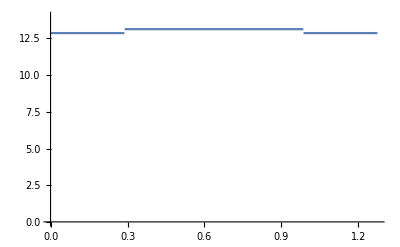

```mathematica
Plot[fEarth[Log[10,FeELOutputDictSI[["kinlist"]][["mχ"]][[2]]],Log[10,FeELOutputDictSI[["kinlist"]][["vχ"]][[1]]],r],{r,0,2Constants`REarth},PlotRange->{0,14}]
```

#### Compute κmin

InterpolatingFunction::dmval: Input value {-30.3516,11.4129} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

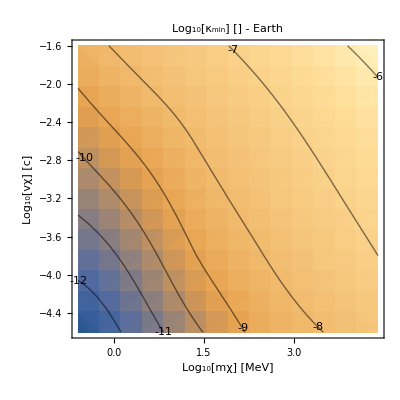

<|table→{{1.78694×10^-13,2.38385×10^-12,7.51191×10^-11,1.83493×10^-9,9.02623×10^-9,2.87489×10^-8},{4.59059×10^-12,6.08682×10^-11,1.77514×10^-9,1.15099×10^-8,4.02946×10^-8,1.27646×10^-7},{1.45468×10^-10,1.62813×10^-9,1.13658×10^-8,4.01435×10^-8,1.26384×10^-7,3.99627×10^-7},{4.61505×10^-9,1.85927×10^-8,5.57513×10^-8,1.76197×10^-7,5.6552×10^-7,1.78877×10^-6}},fκmin→InterpolatingFunction[…],ELdict→<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-31,4.45×10^-31,4.45×10^-31,4.45×10^-31},{4.45×10^-30,4.45×10^-30,4.45×10^-30,4.45×10^-30},{4.45×10^-29,4.45×10^-29,4.45×10^-29,4.45×10^-29},{4.45×10^-28,4.45×10^-28,4.45×10^-28,4.45×10^-28},{4.45×10^-27,4.45×10^-27,4.45×10^-27,4.45×10^-27},{4.45×10^-26,4.45×10^-26,4.45×10^-26,4.45×10^-26}},vχMesh→{{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6}},EnergyLossMesh→{{2.50148×10^14,2.50137×10^13,2.49097×10^12,2.4431×10^11},{1.3628×10^13,1.37102×10^12,2.18775×10^11,2.76683×10^11},{1.37009×10^11,2.224×10^10,8.60681×10^10,2.71456×10^11},{2.22506×10^9,8.76856×10^9,8.47574×10^10,2.71404×10^11},{8.77081×10^8,8.63383×10^9,8.47443×10^10,2.71404×10^11},{8.63601×10^8,8.63248×10^9,8.47441×10^10,2.71404×10^11}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00144809,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19}},fname→FeELOutputDictSI,kinlist→<|mχ→{4.45×10^-31,4.45×10^-30,4.45×10^-29,4.45×10^-28,4.45×10^-27,4.45×10^-26},vχ→{7500.,75000.,750000.,7.5×10^6}|>,meshdims→<|mχ→6,vχ→4|>,timesMesh→{{34.1233,36.3146,35.078,87.8457},{36.9107,33.7301,37.4681,99.9867},{39.2428,36.711,38.7031,76.6925},{39.3594,36.4325,49.0473,145.351},{121.449,99.3101,38.0587,85.4639},{36.0339,44.816,38.6308,83.0538}},totalTime→1409.81|>,fEL→fEarth,vescape→0|>

```mathematica
κminelectrons = κminInterpolationfnofr[FeELOutputDictSI,fEarth,0,(FeELOutputDictSI[["f"]]@Domain),True]
```

```mathematica
SaveIt[NotebookDirectory[]<>"eκminT0",κminelectrons]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\Version_13\ELandKappamin\kappa min\eκminT0.dat

#### Warning sanity check

```mathematica
(*Block[{mχ=Log10[FeELOutputDictSI[["kinlist"]][["mχ"]][[2]]],vχ=Log10[FeELOutputDictSI[["kinlist"]][["vχ"]][[2]]],f=fEarth,κ=10^-10,domain=FeELOutputDictSI[["f"]]@Domain,plot=True,rmax=Constants`REarth},
		(* rmax - [m] default is earth's radius
		Function of κ, solves an ODE for E(r), returning the value at the Earth's diameter. Used this to find κ min (given that E increase when it undershoots)
		*)
		sol=NDSolve[{Ek'[r]==-κ^2 ("JpereV"/.Constants`SIConstRepl) 10^f[mχ,Log[10,Sqrt[Max[2/10^mχ Ek[r],(10^((domain)[[2,1]]))^2]]],r],Ek[0]==1/2 10^mχ  (10^vχ)^2 },Ek,{r,0,2 rmax}];
		If[plot, 
			Print[Plot[((Ek/.First[sol])[r])/("JpereV"/.Constants`SIConstRepl),{r,0,2rmax},AxesLabel->{"r [m]","Eχ(r) [eV]"}]];
														Print[Plot[Log[10,Sqrt[Max[2/10^mχ(Ek/.First[sol])[r],(10^((domain)[[2,1]]))^2]]],{r,0,2rmax},AxesLabel->{"r [m]","v"}]];
		Print[Plot[f[mχ,Log[10,Sqrt[Max[2/10^mχ(Ek/.First[sol])[r],(10^((domain)[[2,1]]))^2]]],r],{r,0,2rmax},AxesLabel->{"r [m]","1/κ^2dE/dr(r) [eV m^-1]"}]]
		];
		Ek[r]/.First[sol]/.r->2 rmax
]*)
```

### With Extrapolation of ν to core T

#### Load EL dicts

```mathematica
(*FeELOutputDictSI =ReadIt[NotebookDirectory[]<>"../compute energy loss/FeELOutputDictSI"];*)
FeELOutputDictSIν =ReadIt[NotebookDirectory[]<>"../compute energy loss/FeELOutputDictSIExtrapolatedν"];
SiO2ELOutputDictSI =ReadIt[NotebookDirectory[]<>"../compute energy loss/SiO2ELOutputDictSI"];
MgOELOutputDictSI =ReadIt[NotebookDirectory[]<>"../compute energy loss/MgOELOutputDictSI"];
```

#### Function Modelling EL in the Earth

```mathematica
fEarthν[mχ_,vχ_,r_]:= Module[{REarth = 6.371 10^6,rmantle =2.885 10^6,rcore},
rcore = REarth - rmantle;
Piecewise[{{FeELOutputDictSIν["f"][mχ,vχ],Abs[r-REarth]<=rcore},{Log[10,0.447 10^SiO2ELOutputDictSI["f"][mχ,vχ]+ 0.387 10^MgOELOutputDictSI["f"][mχ,vχ]],rcore<Abs[r-REarth]<REarth}},0]] (* see overleaf note on silicates, these are fractional abundances in the mantle - ignoring traces substances *)
```

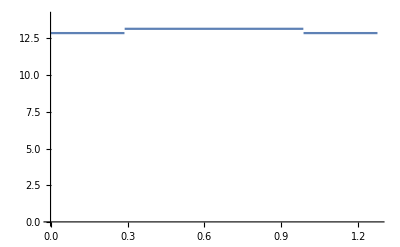

```mathematica
Plot[fEarthν[Log[10,FeELOutputDictSIν[["kinlist"]][["mχ"]][[2]]],Log[10,FeELOutputDictSIν[["kinlist"]][["vχ"]][[1]]],r],{r,0,2Constants`REarth},PlotRange->{0,14}]
```

#### Compute κmin

InterpolatingFunction::dmval: Input value {-30.3516,11.4129} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

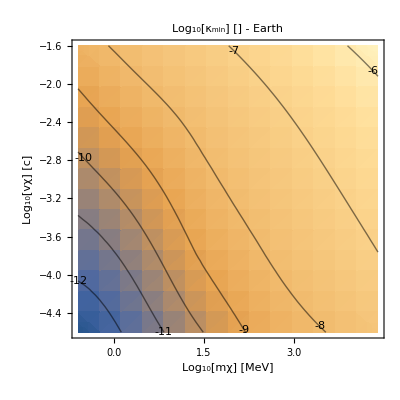

<|table→{{1.81535×10^-13,2.33775×10^-12,7.34824×10^-11,1.77647×10^-9,8.61343×10^-9,2.74249×10^-8},{4.66395×10^-12,5.97361×10^-11,1.72333×10^-9,1.10111×10^-8,3.8455×10^-8,1.21808×10^-7},{1.47793×10^-10,1.59172×10^-9,1.09305×10^-8,3.84197×10^-8,1.21008×10^-7,3.82658×10^-7},{4.68137×10^-9,1.86735×10^-8,5.56862×10^-8,1.76433×10^-7,5.65851×10^-7,1.78967×10^-6}},fκmin→InterpolatingFunction[…],ELdict→<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-31,4.45×10^-31,4.45×10^-31,4.45×10^-31},{4.45×10^-30,4.45×10^-30,4.45×10^-30,4.45×10^-30},{4.45×10^-29,4.45×10^-29,4.45×10^-29,4.45×10^-29},{4.45×10^-28,4.45×10^-28,4.45×10^-28,4.45×10^-28},{4.45×10^-27,4.45×10^-27,4.45×10^-27,4.45×10^-27},{4.45×10^-26,4.45×10^-26,4.45×10^-26,4.45×10^-26}},vχMesh→{{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6}},EnergyLossMesh→{{2.39231×10^14,2.39222×10^13,2.38314×10^12,2.34828×10^11},{1.44137×10^13,1.45039×10^12,2.33078×10^11,2.63485×10^11},{1.4596×10^11,2.44542×10^10,9.65366×10^10,2.582×10^11},{2.4474×10^9,1.01149×10^10,9.51815×10^10,2.58148×10^11},{1.01205×10^9,9.97146×10^9,9.5168×10^10,2.58148×10^11},{9.97701×10^8,9.97003×10^9,9.51678×10^10,2.58148×10^11}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→3.22338×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→2.37219×10^16,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→3.49108×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→1.07806×10^17,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.55522×10^17,Ai→0.00144809,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.23434×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19}},fname→FeELOutputDictSIExtrapolatedν,kinlist→<|mχ→{4.45×10^-31,4.45×10^-30,4.45×10^-29,4.45×10^-28,4.45×10^-27,4.45×10^-26},vχ→{7500.,75000.,750000.,7.5×10^6}|>,meshdims→<|mχ→6,vχ→4|>,timesMesh→{{30.1503,34.9586,34.3105,73.0446},{29.079,31.0345,32.3763,77.7508},{48.9821,84.7536,101.901,177.743},{100.103,98.8504,97.4022,174.916},{103.844,99.571,91.2918,175.768},{95.5082,90.4147,89.6094,176.382}},totalTime→2149.74|>,fEL→fEarthν,vescape→0|>

```mathematica
κminInterpolationfnofr[FeELOutputDictSIν,fEarthν,0,(FeELOutputDictSIν[["f"]]@Domain),True]
```

### With Extrapolation of ν and n to core T

#### Load EL dicts

```mathematica
(*FeELOutputDictSI =ReadIt[NotebookDirectory[]<>"../compute energy loss/FeELOutputDictSI"];*)
FeELOutputDictSIνn =ReadIt[NotebookDirectory[]<>"../compute energy loss/FeELOutputDictSIExtrapolatedνn"];
SiO2ELOutputDictSI =ReadIt[NotebookDirectory[]<>"../compute energy loss/SiO2ELOutputDictSI"];
MgOELOutputDictSI =ReadIt[NotebookDirectory[]<>"../compute energy loss/MgOELOutputDictSI"];
```

#### Function Modelling EL in the Earth

```mathematica
fEarthνn[mχ_,vχ_,r_]:= Module[{REarth = 6.371 10^6,rmantle =2.885 10^6,rcore},
rcore = REarth - rmantle;
Piecewise[{{FeELOutputDictSIνn["f"][mχ,vχ],Abs[r-REarth]<=rcore},{Log[10,0.447 10^SiO2ELOutputDictSI["f"][mχ,vχ]+ 0.387 10^MgOELOutputDictSI["f"][mχ,vχ]],rcore<Abs[r-REarth]<REarth}},0]] (* see overleaf note on silicates, these are fractional abundances in the mantle - ignoring traces substances *)
```

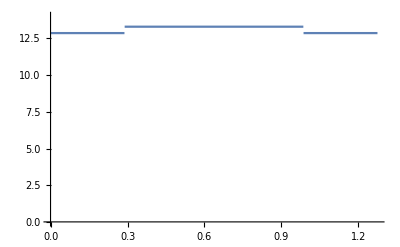

```mathematica
Plot[fEarthνn[Log[10,FeELOutputDictSIνn[["kinlist"]][["mχ"]][[2]]],Log[10,FeELOutputDictSIνn[["kinlist"]][["vχ"]][[1]]],r],{r,0,2Constants`REarth},PlotRange->{0,14}]
```

#### Compute κmin

InterpolatingFunction::dmval: Input value {-30.3516,11.4129} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

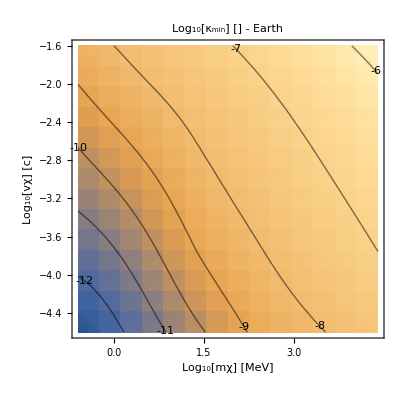

<|table→{{1.54997×10^-13,2.07065×10^-12,6.52496×10^-11,1.65056×10^-9,8.58043×10^-9,2.73678×10^-8},{3.97782×10^-12,5.26553×10^-11,1.57915×10^-9,1.08351×10^-8,3.82342×10^-8,1.21149×10^-7},{1.25935×10^-10,1.46112×10^-9,1.07272×10^-8,3.84421×10^-8,1.20836×10^-7,3.82051×10^-7},{4.02277×10^-9,1.68056×10^-8,5.16272×10^-8,1.61727×10^-7,5.20029×10^-7,1.64502×10^-6}},fκmin→InterpolatingFunction[…],ELdict→<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-31,4.45×10^-31,4.45×10^-31,4.45×10^-31},{4.45×10^-30,4.45×10^-30,4.45×10^-30,4.45×10^-30},{4.45×10^-29,4.45×10^-29,4.45×10^-29,4.45×10^-29},{4.45×10^-28,4.45×10^-28,4.45×10^-28,4.45×10^-28},{4.45×10^-27,4.45×10^-27,4.45×10^-27,4.45×10^-27},{4.45×10^-26,4.45×10^-26,4.45×10^-26,4.45×10^-26}},vχMesh→{{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6},{7500.,75000.,750000.,7.5×10^6}},EnergyLossMesh→{{3.65601×10^14,3.6559×10^13,3.64465×10^12,3.51465×10^11},{2.00459×10^13,2.01392×10^12,2.93633×10^11,3.76392×10^11},{2.01627×10^11,3.00861×10^10,9.98096×10^10,3.67774×10^11},{3.01021×10^9,1.02347×10^10,9.78918×10^10,3.67689×10^11},{1.02378×10^9,1.00362×10^10,9.78726×10^10,3.67688×10^11},{1.00391×10^9,1.00342×10^10,9.78724×10^10,3.67688×10^11}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.73×10^29,qF→1.72381×10^10,vF→1.99629×10^6,μ→1.81524×10^-18,ωp→2.34798×10^16,α→1/137,χ→0.5909,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→24.03,nI→2.1625×10^28,Z→8,M→9.27329×10^-26,EF→1.81524×10^-18,ωi→2.34798×10^16,νi→3.22338×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→3.1922×10^29,qF→2.11432×10^10,vF→2.44853×10^6,μ→2.73085×10^-18,ωp→3.18946×10^16,α→1/137,χ→0.533548,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→36.1507,nI→3.99025×10^28,Z→8,M→9.27329×10^-26,EF→2.73085×10^-18,ωi→3.18946×10^16,νi→2.37219×10^16,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→7.23932×10^29,qF→2.77783×10^10,vF→3.21692×10^6,μ→4.71378×10^-18,ωp→4.8031×10^16,α→1/137,χ→0.465484,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→62.4005,nI→9.04916×10^28,Z→8,M→9.27329×10^-26,EF→4.71378×10^-18,ωi→4.8031×10^16,νi→3.49108×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→5.29788×10^30,qF→5.39313×10^10,vF→6.24561×10^6,μ→1.7768×10^-17,ωp→1.29934×10^17,α→1/137,χ→0.33407,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→235.211,nI→6.62235×10^29,Z→8,M→9.27329×10^-26,EF→1.7768×10^-17,ωi→1.29934×10^17,νi→1.07806×10^17,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→6.91658×10^32,qF→2.73592×10^11,vF→3.16839×10^7,μ→4.57262×10^-16,ωp→1.48463×10^18,α→1/137,χ→0.148322,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→6053.18,nI→8.64572×10^31,Z→8,M→9.27329×10^-26,EF→4.57262×10^-16,ωi→1.48463×10^18,νi→7.55522×10^17,Ai→0.00144809,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→6.66733×10^34,qF→1.25446×10^12,vF→1.45275×10^8,μ→9.61328×10^-15,ωp→1.45763×10^19,α→1/137,χ→0.0692675,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→127260.,nI→8.33416×10^33,Z→8,M→9.27329×10^-26,EF→9.61328×10^-15,ωi→1.45763×10^19,νi→5.23434×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19}},fname→FeELOutputDictSIExtrapolatedνn,kinlist→<|mχ→{4.45×10^-31,4.45×10^-30,4.45×10^-29,4.45×10^-28,4.45×10^-27,4.45×10^-26},vχ→{7500.,75000.,750000.,7.5×10^6}|>,meshdims→<|mχ→6,vχ→4|>,timesMesh→{{82.8791,91.9278,78.8222,106.129},{82.5276,27.4354,31.0729,81.512},{39.3537,38.0932,38.7704,67.4442},{36.3849,33.2845,31.8187,59.7579},{36.7299,34.9863,30.4786,61.0684},{34.9372,33.5805,31.9832,57.966}},totalTime→1248.94|>,fEL→fEarthνn,vescape→0|>

```mathematica
κminInterpolationfnofr[FeELOutputDictSIνn,fEarthνn,0,(FeELOutputDictSIνn[["f"]]@Domain),True]
```

### Without Extrapolation to core T and temperature enhancement

#### Load EL dicts

```mathematica
FeELOutputDictSIEnhanced =ReadIt[NotebookDirectory[]<>"../compute energy loss/FeELOutputDictSIEnhanced"];
SiO2ELOutputDictSIEnhanced =ReadIt[NotebookDirectory[]<>"../compute energy loss/SiO2ELOutputDictSIEnhanced"];
MgOELOutputDictSIEnhanced =ReadIt[NotebookDirectory[]<>"../compute energy loss/MgOELOutputDictSIEnhanced"];
```

#### Function Modelling EL in the Earth

```mathematica
fEarthEnhanced[mχ_,vχ_,r_]:= Module[{REarth = 6.371 10^6,rmantle =2.885 10^6,rcore},
rcore = REarth - rmantle;
Piecewise[{{FeELOutputDictSIEnhanced["f"][mχ,vχ],Abs[r-REarth]<=rcore},{Log[10,0.447 10^SiO2ELOutputDictSIEnhanced["f"][mχ,vχ]+ 0.387 10^MgOELOutputDictSIEnhanced["f"][mχ,vχ]],rcore<Abs[r-REarth]<REarth}},0]] (* see overleaf note on silicates, these are fractional abundances in the mantle - ignoring traces substances *)
```

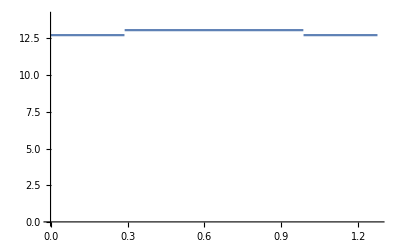

```mathematica
Plot[fEarthEnhanced[Log[10,FeELOutputDictSIEnhanced[["kinlist"]][["mχ"]][[2]]],Log[10,FeELOutputDictSIEnhanced[["kinlist"]][["vχ"]][[1]]],r],{r,0,2Constants`REarth},PlotRange->{0,14}]
```

#### Compute κmin

InterpolatingFunction::dmval: Input value {-32.3516,12.4129} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

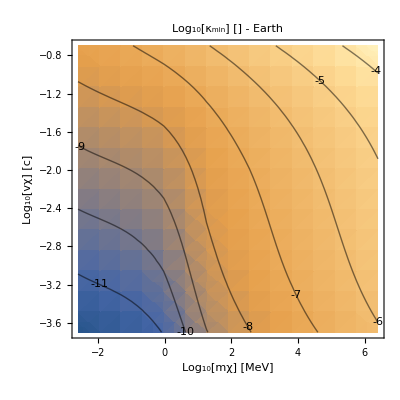

<|table→{{1.39829×10^-12,2.88099×10^-12,1.12097×10^-11,9.1278×10^-10,9.35754×10^-9,4.13643×10^-8,1.81753×10^-7,7.98611×10^-7},{3.72277×10^-11,7.52634×10^-11,3.03417×10^-10,8.12472×10^-9,4.30045×10^-8,1.89243×10^-7,8.31594×10^-7,3.65398×10^-6},{1.17458×10^-9,2.4122×10^-9,5.99747×10^-9,3.75606×10^-8,1.62254×10^-7,7.12755×10^-7,3.13181×10^-6,0.0000138312},{3.52437×10^-8,7.67262×10^-8,2.16762×10^-7,8.98399×10^-7,3.99991×10^-6,0.0000176857,0.00007771,0.000341454}},fκmin→InterpolatingFunction[…],ELdict→<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{2.57498×10^12,2.47858×10^11,2.51307×10^10,2.77097×10^9},{1.16845×10^13,1.16803×10^12,1.13925×10^11,1.14569×10^10},{1.44631×10^13,1.50575×10^12,3.76221×10^11,2.28038×10^10},{4.11163×10^10,7.16323×10^10,3.04212×10^11,2.19452×10^10},{7.00775×10^9,6.82877×10^10,3.04045×10^11,2.19432×10^10},{6.91623×10^9,6.82787×10^10,3.04044×10^11,2.19432×10^10},{6.91598×10^9,6.82787×10^10,3.04044×10^11,2.19432×10^10},{6.91598×10^9,6.82787×10^10,3.04044×10^11,2.19432×10^10}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00193079,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→2.83087×10^-6,ωedgei→1.09893×10^19}},fname→FeELOutputDictSIEnhanced,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{1489.79,1165.11,1272.5,1386.05},{31.3514,32.5184,44.6353,198.696},{24.8404,25.3822,63.9634,371.152},{25.3254,28.7721,56.5477,311.838},{28.2359,29.6444,55.1056,300.827},{28.4212,28.7739,58.2973,292.612},{27.2795,29.3225,58.4821,302.77},{28.0291,30.8888,59.3867,291.653}},totalTime→8178.2|>,fEL→fEarthEnhanced,vescape→11200|>

```mathematica
κminelectronsEnhanced = κminInterpolationfnofr[FeELOutputDictSIEnhanced,fEarthEnhanced,vescape,(FeELOutputDictSIEnhanced[["f"]]@Domain),True]
```

```mathematica
SaveIt[NotebookDirectory[]<>"eκminEnhanced",κminelectronsEnhanced]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\Version_14\ELandKappamin\kappa min\eκminEnhanced.dat

```mathematica
Without Extrapolation to core T and temperature enhancementWithout Extrapolation to core T and temperature enhancement
```

```mathematica
Without Extrapolation to core T and temperature enhancement
```

### Without Extrapolation to core T and temperature enhancement - post fixes

#### Load EL dicts

```mathematica
FeELOutputDictSIEnhanced =ReadIt[NotebookDirectory[]<>"../compute energy loss/FeELOutputDictSIEnhanced"];
SiO2ELOutputDictSIEnhanced =ReadIt[NotebookDirectory[]<>"../compute energy loss/SiO2ELOutputDictSIEnhanced"];
MgOELOutputDictSIEnhanced =ReadIt[NotebookDirectory[]<>"../compute energy loss/MgOELOutputDictSIEnhanced"];
```

```mathematica
SiO2ELOutputDictSIEnhanced[["f"]]=AbsInterpolation[SiO2ELOutputDictSIEnhanced]
MgOELOutputDictSIEnhanced[["f"]]=AbsInterpolation[MgOELOutputDictSIEnhanced]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

#### Function Modelling EL in the Earth

```mathematica
fEarthEnhanced[mχ_,vχ_,r_]:= Module[{REarth = 6.371 10^6,rmantle =2.885 10^6,rcore},
rcore = REarth - rmantle;
Piecewise[{{FeELOutputDictSIEnhanced["f"][mχ,vχ],Abs[r-REarth]<=rcore},{Log[10,0.447 10^SiO2ELOutputDictSIEnhanced["f"][mχ,vχ]+ 0.387 10^MgOELOutputDictSIEnhanced["f"][mχ,vχ]],rcore<Abs[r-REarth]<REarth}},0]] (* see overleaf note on silicates, these are fractional abundances in the mantle - ignoring traces substances *)
```

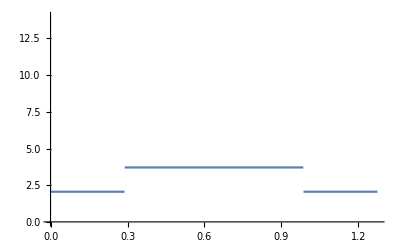

```mathematica
Plot[fEarthEnhanced[Log[10,FeELOutputDictSIEnhanced[["kinlist"]][["mχ"]][[2]]],Log[10,FeELOutputDictSIEnhanced[["kinlist"]][["vχ"]][[1]]],r],{r,0,2Constants`REarth},PlotRange->{0,14}]
```

#### Compute κmin

InterpolatingFunction::dmval: Input value {-32.3516,12.4129} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

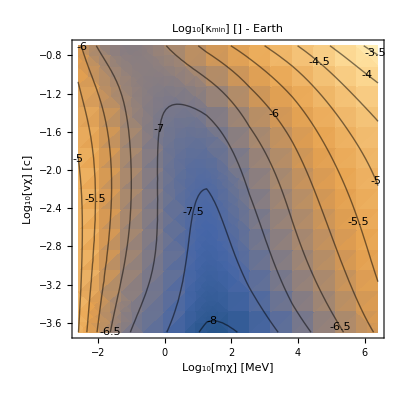

<|table→{{0.000010693,1.59862×10^-7,3.58698×10^-8,8.41381×10^-9,1.29254×10^-8,5.32105×10^-8,2.332×10^-7,1.19571×10^-6},{0.0000159299,4.72327×10^-7,8.00686×10^-8,2.25754×10^-8,6.15202×10^-8,2.64074×10^-7,1.12093×10^-6,5.55414×10^-6},{8.39045×10^-6,5.00529×10^-7,8.54035×10^-8,5.79571×10^-8,2.30414×10^-7,1.01032×10^-6,4.95497×10^-6,0.0000203269},{1.3866×10^-6,1.41939×10^-7,2.91788×10^-7,1.38106×10^-6,5.93459×10^-6,0.0000262006,0.000119919,0.000498932}},fκmin→InterpolatingFunction[…],ELdict→<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{0.0485149,1291.09,183671.,4.8129×10^8},{5135.24,549701.,6.45112×10^8,4.58171×10^9},{1.96071×10^6,4.29186×10^8,9.38163×10^10,8.58682×10^9},{6.16544×10^8,2.49594×10^10,1.47311×10^11,9.36143×10^9},{4.07817×10^9,3.35909×10^10,1.51007×10^11,9.41337×10^9},{4.60511×10^9,3.41212×10^10,1.512×10^11,9.4365×10^9},{4.62448×10^9,3.42631×10^10,9.64951×10^10,9.41994×10^9},{2.85546×10^9,3.40768×10^10,1.51179×10^11,9.45902×10^9}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00108607,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.38712×10^-6,ωedgei→1.09893×10^19}},fname→FeELOutputDictSIEnhanced,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{2403.6,1529.99,779.194,170.133},{1172.4,683.544,132.789,117.841},{419.854,5.32237,58.0866,137.546},{3.30653,72.2412,100.731,249.493},{64.0485,132.771,355.679,573.032},{196.414,379.903,696.574,786.913},{491.869,626.666,905.871,846.886},{825.224,739.606,776.838,892.991}},totalTime→17327.4|>,fEL→fEarthEnhanced,vescape→11200|>

```mathematica
κminelectronsEnhanced = κminInterpolationfnofr[FeELOutputDictSIEnhanced,fEarthEnhanced,vescape,(FeELOutputDictSIEnhanced[["f"]]@Domain),True]
```

```mathematica
SaveIt[NotebookDirectory[]<>"eκminEnhanced",κminelectronsEnhanced]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\ELandKappamin\kappa min\eκminEnhanced.dat

```mathematica
Without Extrapolation to core T and temperature enhancementWithout Extrapolation to core T and temperature enhancement
```

and^2 core^2 enhancement enhancementWithout Extrapolation^2 T^2 temperature^2 to^2 Without

```mathematica
Without Extrapolation to core T and temperature enhancement
```

and core enhancement Extrapolation T temperature to Without